```mathematica
X =Import["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\PeptideDataOut.m"];
```

```mathematica
NEME = Import["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\SeqAny.csv"];
NemFindID = Table[If[NEME[[i]][[3]] == 1,NEME[[i]][[1]], Nothing],{i,1,Length[NEME]}];
```

```mathematica
PEPID = Import["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\PEPIDS.tsv"];
```

```mathematica
PEPID;
```

```mathematica
d=Dimensions[X][[1]];
Xdata = X[[1;;d-1]];
Nt = X[[d]];
Xdata;
```

```mathematica
Xdata[[1]]
```

{2015,3292,3719,4835}

```mathematica
FitList = Table[0,{i, 1, 1061}];
PioList= Table[0,{i, 1, 1061}];
PooledList = Table[0,{i, 1, 1061}];
MFCest = Table[1,{i,1,4}];
FitSeq = Table[0,{i, 1, 1061}];
ErrorCheck = {};
```

```mathematica
ProdMeanFIT[MFCest_,t_] :=
∏_(k=1)^t MFCest[[k]];
```

```mathematica
SolvePio[ω_,nit_,Nt_,MFCest_] :=

 (∑_(t=1)^4 nit[[t]]*t)/(∑_(t=1)^4 ((Nt[[t]]*ω^t)*t)/ProdMeanFIT[MFCest,t])
```

```mathematica
PolyFitCoe[nit_,Nt_,MFCest_,t_] :=
 (Nt[[t]]/ProdMeanFIT[MFCest,t])∑_(k=1)^4 (nit[[k]]*(t-k))
```

```mathematica
PolySolveFIT[nit_,Nt_,MFCest_]:=

Module[{k,Ct},
Ct = Table[0,{i,1,4}];
Do[
Ct[[k]] = PolyFitCoe[nit,Nt,MFCest,k],
{k,1,4}
];
Return[Solve[∑_(k=1)^4 Ct[[k]] ω^(k-1) == 0,ω, Reals]]
]
```

```mathematica
LikelihoodTuple[ω_,nit_,Nt_,MFCest_] :=
Module[{i,t,k,kpio,p, likeList,bestCheck},
likeList = Table[0,{k,1,Length[ω]}];

Do[

kpio = SolvePio[ω[[i]],nit,Nt,MFCest];
likeList[[i]] =∑_(t=1)^4 (nit[[t]](Log[kpio]+t*Log[ω[[i]]]-Log[ProdMeanFIT[MFCest,t]])-(Nt[[t]]*kpio*ω[[i]]^t)/ProdMeanFIT[MFCest,t]),
{i,1,Length[ω]}
];
If[nit == {2015,3292,3719,4835},Print[likeList],Nothing];
p = Position[likeList,Max[likeList]][[1]];
bestCheck = {ω[[p]][[1]],kpio};
Return[bestCheck];
]
```

```mathematica
PioCorrection[Xdata_,Nt_] :=
Module[{i,j,k,t,tempPi,tempIndex,lm},

tempPi = Table[{t,Sum[Xdata[[i]][[t]],{i,1,Length[Xdata]}]/Nt[[t]]},{t,1,Length[Nt]}];
lm = LinearModelFit[tempPi,x,x];
Return[lm[0]];
]
```

```mathematica
MeanFitCorrectionEst[Xdata_,Nt_,PioList_,FitList_]:=
Module[{i,k,j,t,n,g,ks,ps,fitCorrectL,pioCorr},
fitCorrectL = Table[0,{k,1,4}];

ps = Table[(∑_(i=1)^Length[Xdata] Xdata[[i]][[t]])/Nt[[t]],{t,1,4}];
ks = Table[∑_(j=1)^Length[Xdata] FitList[[j]]^t*PioList[[j]],{t,1,4}];

fitCorrectL[[1]] = (ks[[1]]/ps[[1]]); 
Do[
fitCorrectL[[t]] =ps[[t-1]]/ps[[t]]*ks[[t]]/ks[[t-1]],
{t,2,4}];
Return[fitCorrectL]
]
```

```mathematica
FitSeqFun[PooledList_,MFCest_]:=
Module[{i,j,l,k,FitSeq,Temp},
FitSeq = Table[0,{i,1,Length[PooledList]}];

Do[
Temp = Table[0,{j,1,4}];
Do[
Temp[[l]] = (PooledList[[k]][[1]])^l/ProdMeanFIT[MFCest,l],
{l,1,4}];
FitSeq [[k]]=Temp,
{k,1,Length[PooledList]}];
Return[FitSeq]
]
```

```mathematica
Weight[Sest_,Pest_,Nt_,MFCest_] := Pest *Sum[((t/Sest)^2)*(Nt[[t]]*Sest^t)*(1/ProdMeanFIT[MFCest,t]),{t,1,4}]
```

```mathematica
MassLogLike[Sest_,Pest_,Xdata_,Nt_,MFCest_] :=
∑_(t=1)^4 ∑_(i=1)^Length[Xdata] ((Xdata[[i]][[t]]*(Log[(Pest[[i]]*Sest[[i]]^t)/ProdMeanFIT[MFCest,t]]))-(Nt[[t]]*Pest[[i]] Sest[[i]]^t/ProdMeanFIT[MFCest,t]))
```

```mathematica
Module[{i,n,k,m,pioNorm},
Do[
XdataT = Table[ If[Sum[If[Xdata[[k]][[t]] == 0,1,0],{t,1,4}]<3,Xdata[[k]],Nothing],{k,1,Length[Xdata]}];
FitList = Table[0,{i, 1, Length[XdataT]}];
PioList= Table[0,{i, 1, Length[XdataT]}];
PooledList = Table[0,{i, 1, Length[XdataT]}];
Do[
nit = XdataT[[i]];

fitEsts = N[ω/.PolySolveFIT[nit,Nt,MFCest]];
PooledList[[i]] = LikelihoodTuple[fitEsts,nit,Nt,MFCest],
{i,1,Length[XdataT]}
];
PioList = Table[PooledList[[i]][[2]],{i,1,Length[PooledList]}];
FitList = Table[PooledList[[i]][[1]],{i,1,Length[PooledList]}];

West= Table[0,{i, 1, Length[FitList]}];
Do[
West[[z]] = Weight[FitList[[z]],PioList[[z]],Nt,MFCest],
{z,1,Length[FitList]}
];
Print[West[[1;;30]]];

pioNorm = Sum[PioList[[n]],{n,1,Length[PioList]}];
PioList = (PioList/pioNorm)*PioCorrection[Xdata,Nt];
Print[MassLogLike[FitList,PioList,XdataT,Nt,MFCest]];
MFCest = MeanFitCorrectionEst[XdataT,Nt,PioList,FitList];
Print[MFCest],
{m,1,10}
]

]
```

{-75533.5}

{77215.8,60636.7,63483.3,95923.5,74019.5,53428.1,50327.3,53505.6,46006.7,58092.,47950.8,39869.4,53307.4,51266.2,42958.7,44481.2,39170.7,37060.2,40432.4,51512.8,48875.4,48815.2,35100.1,38656.6,31346.7,43454.8,33438.6,36806.1,43024.3,36215.5}

-6.25828×10^6

{0.456265,0.778306,1.06586,1.19152}

{-75369.4}

{72735.2,55377.9,58694.2,92962.,70365.9,49395.6,46694.,49592.2,42858.9,54506.7,44169.,37153.4,50041.,52335.3,39823.9,42156.7,36560.4,34952.9,38999.8,50496.,49054.,47353.5,32020.3,37840.6,29024.,43438.3,31207.,33734.6,51493.9,33380.1}

-6.00962×10^6

{0.397189,0.744643,1.07838,1.22776}

{-75355.8}

{71904.6,54428.1,57819.9,92402.4,69684.,48659.5,46028.7,48876.3,42280.6,53844.1,43480.8,36654.3,49437.1,52551.4,39250.3,41723.8,36080.1,34561.9,38729.8,50303.3,49092.3,47077.2,31464.5,37686.,28599.5,43438.,30796.4,33178.1,53337.1,32863.9}

-5.99988×10^6

{0.386512,0.738132,1.08094,1.23499}

{-75353.7}

{71738.7,54239.4,57645.9,92290.,69547.5,48512.9,45896.2,48733.7,42165.3,53711.8,43343.9,36554.8,49316.6,52595.1,39136.1,41637.2,35984.3,34483.8,38675.6,50264.5,49100.,47021.7,31354.2,37654.8,28515.,43437.9,30714.6,33067.5,53717.1,32761.2}

-5.99949×10^6

{0.38439,0.736821,1.08146,1.23645}

{-75353.2}

{71705.,54201.2,57610.6,92267.2,69519.8,48483.2,45869.4,48704.8,42141.9,53685.,43316.2,36534.6,49292.2,52603.9,39112.9,41619.6,35964.9,34468.,38664.6,50256.6,49101.5,47010.4,31331.8,37648.5,28497.9,43437.8,30698.,33045.1,53794.7,32740.4}

-5.99947×10^6

{0.383961,0.736554,1.08157,1.23675}

{-75353.2}

{71698.2,54193.5,57603.5,92262.6,69514.2,48477.2,45863.9,48699.,42137.2,53679.6,43310.5,36530.5,49287.2,52605.7,39108.2,41616.,35961.,34464.7,38662.3,50255.,49101.8,47008.1,31327.3,37647.2,28494.4,43437.8,30694.6,33040.5,53810.4,32736.1}

-5.99947×10^6

{0.383873,0.7365,1.08159,1.23681}

{-75353.1}

{71696.8,54191.9,57602.,92261.6,69513.,48476.,45862.8,48697.8,42136.2,53678.5,43309.4,36529.7,49286.2,52606.1,39107.3,41615.3,35960.2,34464.1,38661.9,50254.7,49101.9,47007.6,31326.4,37647.,28493.7,43437.8,30693.9,33039.6,53813.6,32735.3}

-5.99947×10^6

{0.383855,0.736489,1.0816,1.23682}

{-75353.1}

{71696.5,54191.6,57601.7,92261.4,69512.8,48475.7,45862.6,48697.5,42136.,53678.3,43309.1,36529.5,49286.,52606.2,39107.1,41615.2,35960.,34464.,38661.8,50254.6,49101.9,47007.5,31326.2,37646.9,28493.5,43437.8,30693.8,33039.4,53814.3,32735.1}

-5.99947×10^6

{0.383852,0.736487,1.0816,1.23682}

{-75353.1}

{71696.5,54191.5,57601.6,92261.4,69512.8,48475.7,45862.5,48697.5,42136.,53678.2,43309.1,36529.5,49285.9,52606.2,39107.,41615.1,35960.,34463.9,38661.8,50254.6,49101.9,47007.5,31326.2,37646.9,28493.5,43437.8,30693.7,33039.4,53814.4,32735.1}

-5.99947×10^6

{0.383851,0.736487,1.0816,1.23682}

{-75353.1}

{71696.5,54191.5,57601.6,92261.4,69512.8,48475.7,45862.5,48697.5,42136.,53678.2,43309.1,36529.4,49285.9,52606.2,39107.,41615.1,35960.,34463.9,38661.8,50254.6,49101.9,47007.5,31326.2,37646.9,28493.5,43437.8,30693.7,33039.4,53814.5,32735.1}

-5.99947×10^6

{0.383851,0.736486,1.0816,1.23682}

```mathematica
Sum[If[FitList[[i]] > 1,1,0], {i,1,Length[FitList]}]
```

517

```mathematica
MFCest
```

{0.383851,0.736486,1.0816,1.23682}

```mathematica
DELPeptideIDList = Table[ If[Sum[If[Xdata[[k]][[t]] == 0,1,0],{t,1,4}]<3,PEPID[[k+1]][[2]],Nothing],{k,1,Length[Xdata]}];
```

```mathematica
OutputTable = Table[{DELPeptideIDList[[i]],FitList[[i]],West[[i]]},{i,1,Length[FitList]}];
```

```mathematica
OutputTable = Insert[OutputTable,{"PEP ID","FIT EST","WEIGHT"},1];
```

```mathematica
Export["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\MFCOutput.tsv",OutputTable,"TSV"]
```

C:\Users\decre\Desktop\Masle Lab R\Python Sorting\MFCOutput.tsv

```mathematica
Export["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\HistogramP1.tsv",data1,"TSV"]
Export["C:\\Users\\decre\\Desktop\\Masle Lab R\\Python Sorting\\HistogramP2.tsv",data2,"TSV"]
```

C:\Users\decre\Desktop\Masle Lab R\Python Sorting\HistogramP1.tsv

C:\Users\decre\Desktop\Masle Lab R\Python Sorting\HistogramP2.tsv

```mathematica
OutputTable;
```

```mathematica
NemeFitList = Table[0,{i, 1, Length[NemFindID]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[NemFindID]
```

277

```mathematica
FitnessCatch = Table[If[OutputTable[[i]][[2]] > 1,{OutputTable[[i]][[1]],OutputTable[[i]][[2]]},Nothing],{i,2,Length[OutputTable]}];
```

```mathematica
FitnessCatch;
```

```mathematica
Length[FitnessCatch]
```

517

```mathematica
NemFindID[[1]][[1]]
```

Part::partd: Part specification PEPNR00000000002⟦1⟧ is longer than depth of object.

PEPNR00000000002⟦1⟧

```mathematica
Module [{i,j},
Do[
Do[
NemeFitList[[i]] = If[NemFindID[[i]] == OutputTable[[j]][[1]],{NemFindID[[i]],OutputTable[[j]][[2]]},NemeFitList[[i]]],
{j,1,Length[OutputTable]}
],
{i,1,Length[NemFindID]}


]
]
NemeFitList;
```

```mathematica
ErrorNem = Table[If[NemeFitList[[i]][[2]] < 1,NemeFitList[[i]],Nothing],{i,1,Length[NemeFitList]}]
```

{{PEPNR00000000665,0.988891},{PEPNR00000000933,0.942257},{PEPNR00000001049,0.951331}}

```mathematica
NemeFitList;
```

```mathematica
data1 = Table[FitnessCatch[[i]][[2]],{i,1,Length[FitnessCatch]}];
data2 = Table[NemeFitList[[i]][[2]],{i,1,Length[NemeFitList]}];
```

```mathematica
data2;
```

```mathematica
NemeFitList[[1]][[2]]
```

1.32898

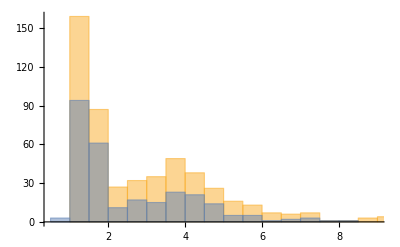

```mathematica
Histogram[{data1,data2}]
```

```mathematica
t = {0,1,2,3}
```

{0,1,2,3}

```mathematica
Plot
```

Plot

```mathematica
parabola=Fit[MFCest,{1,x,x^2},x]
line=Fit[MFCest,{1,x},x]
exp = Fit[MFCest,{1,Log[x]},x]
```

-0.113079+0.537164 x-0.0493524 x^2

0.133683+0.290402 x

0.360494+0.628302 Log[x]

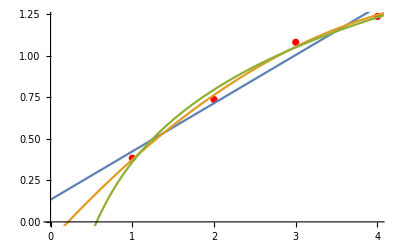

```mathematica
Show[ListPlot[MFCest,PlotStyle->Red],Plot[{line,parabola,exp},{x,0,5}]]
```

```mathematica
MFCest
```

{0.383851,0.736486,1.0816,1.23682}

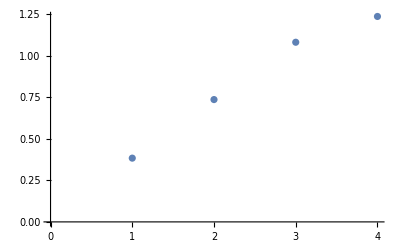

```mathematica
ListPlot[MFCest]
```

```mathematica
NemFindID[[1]] == OutputTable[[1]][[1]]
```

False

```mathematica
OutputTable;
```

```mathematica
NemFindID;
```